Definitions

```mathematica
lisaXML[filename_]:=
Cases[Import[filename],XMLElement["XSIL",___]][[1]]/.
XMLElement[head_,attrs_,content_]->
XMLElement[head,attrs,Join[content,{XMLElement["Filename",{},filename]}]];
```

```mathematica
getLISASources[lisaxml_]:=Map[
Function[src,
LISASource[Join[
Cases[src,{"Name"->srcname_,___}->("Name"->srcname)],
Cases[src[[3]],XMLElement["Param",{"Name"->parname_,___},{parval_}]->(parname->parval)]
]]
],
Cases[lisaxml[[3]],XMLElement["XSIL",{"Type"->"SourceData",___},sources___]->sources][[1]]
];
```

```mathematica
convertNumber[x_]:=StringReplace[x,RegularExpression["([+\-0-9\.]*)[eE]([+\-0-9]*)"]->"$1*10^$2"];
```

```mathematica
LISASource[rules_][par_]:=ToExpression[convertNumber[par/.rules]];
LISASource[rules_][par_,String]:=par/.rules;
```

```mathematica
LISASource/:Print[LISASource[rules_]]:=TableForm[Map[{#[[1]],#[[2]]}&,rules]];
```

```mathematica
sortTimes[srcs_]:=Sort[srcs,#1["CoalescenceTime"]<#2["CoalescenceTime"]&];
sortCentralTimes[srcs_]:=Sort[srcs,#1["CentralTime"]<#2["CentralTime"]&];
```

```mathematica
parDiff[str1_,str2_]:=str1-str2;

fracDiff[str1_,str2_]:=ToString[PaddedForm[100*(str1-str2)/str2,{5,2}]]<>"%";
fracDiff[str1_,str2_,par_]:=
ToString[PaddedForm[100*
If[par=="EclipticLongitude",
(str1-str2)/(2Pi),
If[par=="EclipticLatitude" || par=="Polarization",
(str1-str2)/Pi,
(str1-str2)/str2]
],
{5,2}]]<>"%";
```

```mathematica
LISASource/:Diff[LISASource[rules1_],LISASource[rules2_],vars_]:=TableForm[
Map[{#[[1]],#[[2]],LISASource[rules2][#[[1]],String],
parDiff[LISASource[rules2][#[[1]]],ToExpression[convertNumber[#[[2]]]]],
fracDiff[LISASource[rules2][#[[1]]],ToExpression[convertNumber[#[[2]]]],#[[1]]]}&,
Select[rules1,MemberQ[vars,#[[1]]]&]
]
];
```

Load TDI files

```mathematica
parseTDIObservable[{tdiname_,tdiobs_},file_]:=Module[{pars1,timeseries,pars2,array,dims,stream},
pars1=Cases[tdiobs,XMLElement["Param",{"Name"->parname_,___},{parval_}]->(parname->parval)];

timeseries=Cases[tdiobs,XMLElement["XSIL",{"Name"->name_,"Type"->"TimeSeries"},content___]->content][[1]];
pars2=Cases[timeseries,XMLElement["Param",{"Name"->parname_,___},{parval_}]->(parname->parval)];

array=Cases[timeseries,XMLElement["Array",{"Name"->name_,___},content___]->content][[1]];
dims=Cases[array,XMLElement["Dim",{"Name"->dimname_},{dimval_}]->(dimname->dimval)];

stream=Cases[array,XMLElement["Stream",{"Type"->type_,"Encoding"->encoding_},{filename_}]->("Stream"->{filename,type,encoding})];

TDIObservable[Join[{"Name"->tdiname},pars1,pars2,dims,stream,{file}]]
];
```

```mathematica
getTDIData[lisaxml_]:=Module[{filename,tdidata,tdiobs},
filename=Cases[lisaxml[[3]],XMLElement["Filename",{},file_]->("Filename"->file)][[1]];

tdidata=Cases[lisaxml[[3]],XMLElement["XSIL",{"Type"->"TDIData",___},content___]->content][[1]];
tdiobs=Cases[tdidata,XMLElement["XSIL",{"Name"->name_,"Type"->"TDIObservable"},content___]->{name,content}];

Map[parseTDIObservable[#,filename]&,tdiobs]
];
```

```mathematica
TDIObservable[rules_][par_]:=ToExpression[convertNumber[par]/.rules];
TDIObservable[rules_][par_,String]:=par/.rules;
```

```mathematica
TDIObservable[rules_]["Data"]:=Module[{filename,type,encoding,data},
{filename,type,encoding}=TDIObservable[rules]["Stream",String];
filename=DirectoryName[TDIObservable[rules]["Filename",String]]<>filename;

data=If[StringFreeQ[encoding,"BigEndian"], (* LittleEndian *)
Import[filename,"Real64",ByteOrdering->-1],
Import[filename,"Real64",ByteOrdering->1]
];

Transpose[Partition[data,TDIObservable[rules]["Records"]]]
];
```

```mathematica
ch32=lisaXML["/Users/vallis/Desktop/training-3/challenge3.2-training-nonoise-frequency.xml"];
```

```mathematica
Timing[a=tdi1["Data"];]
```

{4.23144,Null}

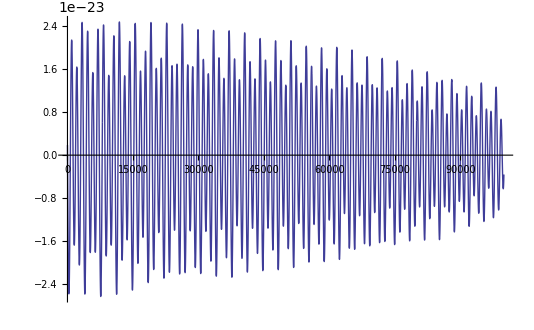

```mathematica
ListPlot[a[[2,Range[100000]]],PlotJoined->True]
```

Load parameter sets (SMBH)

```mathematica
sol32=getLISASources[lisaXML["http://www.tapir.caltech.edu/~mldc/results3/challenge3.2-key.xml"]];
```

```mathematica
MapThread[Set[#1,getLISASources[lisaXML[#2]]]&,
{{jpl32,cam32,cam32b,gsfc32,mt32},
{"http://www.tapir.caltech.edu/~mldc/results3/JPLCITNWU-3.2-090430-230756.xml",
"http://www.tapir.caltech.edu/~mldc/results3/AEICamb-3.2-090430-110034.xml",
"http://www.tapir.caltech.edu/~mldc/results3/CambAEI-3.2-090430-064232.xml",
"http://www.tapir.caltech.edu/~mldc/results3/GSFC-3.2-090430-170214.xml",
"http://www.tapir.caltech.edu/~mldc/results3/MTGWAGAPC-3.2-090430-230137.xml"}}];
```

Note the last two are Galaxy entries

```mathematica
sol32=sortTimes[sol32];
Map[#["CoalescenceTime"]&,sol32][[Range[5]]]
```

{5.74594×10^6,3.2961×10^7,3.65131×10^7,6.48299×10^7,7.14888×10^7}

```mathematica
vars={"EclipticLatitude","EclipticLongitude","PolarAngleOfSpin1","PolarAngleOfSpin2","AzimuthalAngleOfSpin1","AzimuthalAngleOfSpin2","Spin1","Spin2","Mass1","Mass2","CoalescenceTime","PhaseAtCoalescence","InitialPolarAngleL","InitialAzimuthalAngleL","Distance"};
```

Evaluate parameter errors (SMBH)

```mathematica
vars={"EclipticLatitude","EclipticLongitude","Mass1","Mass2"};
```

## JPL

```mathematica
jpl32=sortTimes[jpl32];
Map[#["CoalescenceTime"]&,jpl32]
```

{5.74591×10^6,3.29607×10^7,3.65128×10^7,6.48409×10^7}

### MLDC 3.2.1-3.2.4 (sources sorted by CoalescenceTime)

```mathematica
Do[Print[Diff[sol32[[i]],jpl32[[i]],vars]],{i,4}]
```

EclipticLatitude | 0.745898975433 | 0.284720516085 | -0.461178 |  -14.68%
EclipticLongitude | 3.65766816338 | 3.55808294749 | -0.0995852 |   -1.58%
Mass1 | 2001908.74581 | 2039057.96812 | 37149.2 |    1.86%
Mass2 | 532853.349434 | 525544.497088 | -7308.85 |   -1.37%

EclipticLatitude | 1.40392832706 | 1.2473154136 | -0.156613 |   -4.99%
EclipticLongitude | 3.15346046206 | 2.63745253015 | -0.516008 |   -8.21%
Mass1 | 3640964.6489 | 3601925.97126 | -39038.7 |   -1.07%
Mass2 | 1972020.16503 | 1985260.99592 | 13240.8 |    0.67%

EclipticLatitude | 0.430204764682 | 0.438539624977 | 0.00833486 |    0.27%
EclipticLongitude | 6.07354944447 | 6.14955157394 | 0.0760021 |    1.21%
Mass1 | 3892496.72406 | 3780037.23095 | -112459. |   -2.89%
Mass2 | 1117379.34205 | 1137768.07559 | 20388.7 |    1.82%

EclipticLatitude | 0.885442535072 | 0.934070143881 | 0.0486276 |    1.55%
EclipticLongitude | 3.7740365225 | 3.44663787108 | -0.327399 |   -5.21%
Mass1 | 2747087.40822 | 3112107.95494 | 365021. |   13.29%
Mass2 | 1786054.45701 | 1605293.3172 | -180761. |  -10.12%

## CAM

```mathematica
cam32=sortTimes[cam32];
Map[#["CoalescenceTime"]&,cam32]
```

{5.74587×10^6,5.74594×10^6,5.74594×10^6,5.74597×10^6,5.74657×10^6,3.29611×10^7,3.29611×10^7,3.29612×10^7,3.29612×10^7,3.65128×10^7,3.65128×10^7,3.65128×10^7,3.65129×10^7,3.65132×10^7,3.65132×10^7,6.48215×10^7,6.4822×10^7,6.48485×10^7,6.48681×10^7,7.14065×10^7,7.15323×10^7}

```mathematica
Map[#["Probability"]&,cam32]
```

{0.199918,0.200022,0.200042,0.199993,0.200025,0.249981,0.250037,0.25001,0.249972,0.167013,0.166636,0.166659,0.166459,0.166637,0.166596,0.250484,0.248668,0.250712,0.250136,0.468504,0.531496}

### MLDC 3.2.1

```mathematica
Do[Print[Diff[sol32[[1]],cam32[[i]],vars]],{i,1,5}]
```

EclipticLatitude | 0.745898975433 | 0.581555371588 | -0.164344 |   -5.23%
EclipticLongitude | 3.65766816338 | 3.81084992126 | 0.153182 |    2.44%
Mass1 | 2001908.74581 | 2003124.04527 | 1215.3 |    0.06%
Mass2 | 532853.349434 | 532619.876223 | -233.473 |   -0.04%

EclipticLatitude | 0.745898975433 | 0.65322213007 | -0.0926768 |   -2.95%
EclipticLongitude | 3.65766816338 | 3.63626106882 | -0.0214071 |   -0.34%
Mass1 | 2001908.74581 | 1999058.59911 | -2850.15 |   -0.14%
Mass2 | 532853.349434 | 533481.129434 | 627.78 |    0.12%

EclipticLatitude | 0.745898975433 | 0.67383531144 | -0.0720637 |   -2.29%
EclipticLongitude | 3.65766816338 | 3.64814960134 | -0.00951856 |   -0.15%
Mass1 | 2001908.74581 | 1994345.74781 | -7563. |   -0.38%
Mass2 | 532853.349434 | 534495.201841 | 1641.85 |    0.31%

EclipticLatitude | 0.745898975433 | 0.757438540063 | 0.0115396 |    0.37%
EclipticLongitude | 3.65766816338 | 3.6274405447 | -0.0302276 |   -0.48%
Mass1 | 2001908.74581 | 1989902.53592 | -12006.2 |   -0.60%
Mass2 | 532853.349434 | 535402.46075 | 2549.11 |    0.48%

EclipticLatitude | 0.745898975433 | -0.706145274795 | -1.45204 |  -46.22%
EclipticLongitude | 3.65766816338 | 0.494524602341 | -3.16314 |  -50.34%
Mass1 | 2001908.74581 | 1990800.52368 | -11108.2 |   -0.55%
Mass2 | 532853.349434 | 535284.043679 | 2430.69 |    0.46%

### MLDC 3.2.2

```mathematica
Do[Print[Diff[sol32[[2]],cam32[[i]],vars]],{i,6,9}]
```

EclipticLatitude | 1.40392832706 | 1.43954309287 | 0.0356148 |    1.13%
EclipticLongitude | 3.15346046206 | 2.7928463874 | -0.360614 |   -5.74%
Mass1 | 3640964.6489 | 3571057.42945 | -69907.2 |   -1.92%
Mass2 | 1972020.16503 | 2006421.42378 | 34401.3 |    1.74%

EclipticLatitude | 1.40392832706 | -1.44654198701 | -2.85047 |  -90.73%
EclipticLongitude | 3.15346046206 | 5.89834200478 | 2.74488 |   43.69%
Mass1 | 3640964.6489 | 3644006.80788 | 3042.16 |    0.08%
Mass2 | 1972020.16503 | 1970225.51122 | -1794.65 |   -0.09%

EclipticLatitude | 1.40392832706 | -1.42367573697 | -2.8276 |  -90.01%
EclipticLongitude | 3.15346046206 | 0.12339146243 | -3.03007 |  -48.23%
Mass1 | 3640964.6489 | 3570782.08909 | -70182.6 |   -1.93%
Mass2 | 1972020.16503 | 2006266.72204 | 34246.6 |    1.74%

EclipticLatitude | 1.40392832706 | -1.37770354876 | -2.78163 |  -88.54%
EclipticLongitude | 3.15346046206 | 0.319168747808 | -2.83429 |  -45.11%
Mass1 | 3640964.6489 | 3566131.03681 | -74833.6 |   -2.06%
Mass2 | 1972020.16503 | 2008826.96116 | 36806.8 |    1.87%

### MLDC 3.2.3

```mathematica
Do[Print[Diff[sol32[[3]],cam32[[i]],vars]],{i,10,15}]
```

EclipticLatitude | 0.430204764682 | -0.432037900213 | -0.862243 |  -27.45%
EclipticLongitude | 6.07354944447 | 2.93474177543 | -3.13881 |  -49.96%
Mass1 | 3892496.72406 | 3842705.45662 | -49791.3 |   -1.28%
Mass2 | 1117379.34205 | 1128526.29447 | 11147. |    1.00%

EclipticLatitude | 0.430204764682 | -0.432469338893 | -0.862674 |  -27.46%
EclipticLongitude | 6.07354944447 | 2.93512527648 | -3.13842 |  -49.95%
Mass1 | 3892496.72406 | 3774677.45972 | -117819. |   -3.03%
Mass2 | 1117379.34205 | 1144719.75141 | 27340.4 |    2.45%

EclipticLatitude | 0.430204764682 | -0.432181713107 | -0.862386 |  -27.45%
EclipticLongitude | 6.07354944447 | 2.93407064859 | -3.13948 |  -49.97%
Mass1 | 3892496.72406 | 3832241.16348 | -60255.6 |   -1.55%
Mass2 | 1117379.34205 | 1131106.09114 | 13726.7 |    1.23%

EclipticLatitude | 0.430204764682 | -0.442823867209 | -0.873029 |  -27.79%
EclipticLongitude | 6.07354944447 | 2.93349539702 | -3.14005 |  -49.98%
Mass1 | 3892496.72406 | 3837694.56449 | -54802.2 |   -1.41%
Mass2 | 1117379.34205 | 1129561.84513 | 12182.5 |    1.09%

EclipticLatitude | 0.430204764682 | 0.432421401262 | 0.00221664 |    0.07%
EclipticLongitude | 6.07354944447 | 6.07628649139 | 0.00273705 |    0.04%
Mass1 | 3892496.72406 | 3827869.68409 | -64627. |   -1.66%
Mass2 | 1117379.34205 | 1132465.757 | 15086.4 |    1.35%

EclipticLatitude | 0.430204764682 | 0.432229650738 | 0.00202489 |    0.06%
EclipticLongitude | 6.07354944447 | 6.07360198405 | 0.0000525396 |    0.00%
Mass1 | 3892496.72406 | 3863411.24106 | -29085.5 |   -0.75%
Mass2 | 1117379.34205 | 1124205.69163 | 6826.35 |    0.61%

### MLDC 3.2.4

```mathematica
Do[Print[Diff[sol32[[4]],cam32[[i]],vars]],{i,16,19}]
```

EclipticLatitude | 0.885442535072 | 1.06399969089 | 0.178557 |    5.68%
EclipticLongitude | 3.7740365225 | 3.70346962762 | -0.0705669 |   -1.12%
Mass1 | 2747087.40822 | 2816581.32868 | 69493.9 |    2.53%
Mass2 | 1786054.45701 | 1736716.43606 | -49338. |   -2.76%

EclipticLatitude | 0.885442535072 | -0.493925381953 | -1.37937 |  -43.91%
EclipticLongitude | 3.7740365225 | 6.18913167498 | 2.4151 |   38.44%
Mass1 | 2747087.40822 | 3350143.30847 | 603056. |   21.95%
Mass2 | 1786054.45701 | 1477873.70529 | -308181. |  -17.25%

EclipticLatitude | 0.885442535072 | 0.404042323656 | -0.4814 |  -15.32%
EclipticLongitude | 3.7740365225 | 2.96532598407 | -0.808711 |  -12.87%
Mass1 | 2747087.40822 | 3193464.21242 | 446377. |   16.25%
Mass2 | 1786054.45701 | 1553679.35237 | -232375. |  -13.01%

EclipticLatitude | 0.885442535072 | -0.988354109032 | -1.8738 |  -59.64%
EclipticLongitude | 3.7740365225 | 0.435081939788 | -3.33895 |  -53.14%
Mass1 | 2747087.40822 | 3330741.27462 | 583654. |   21.25%
Mass2 | 1786054.45701 | 1536529.74733 | -249525. |  -13.97%

### MLDC 3.2.5

```mathematica
Do[Print[Diff[sol32[[5]],cam32[[i]],vars]],{i,20,21}]
```

EclipticLatitude | -0.944585436651 | -0.978239 | -0.0336536 |   -1.07%
EclipticLongitude | 1.36770589074 | 1.39403 | 0.0263241 |    0.42%
Mass1 | 4480431.5681 | 3914768.26975 | -565663. |  -12.63%
Mass2 | 1275478.03823 | 1396582.83036 | 121105. |    9.49%

EclipticLatitude | -0.944585436651 | 0.871578 | 1.81616 |   57.81%
EclipticLongitude | 1.36770589074 | 4.63384 | 3.26613 |   51.98%
Mass1 | 4480431.5681 | 4780453.86239 | 300022. |    6.70%
Mass2 | 1275478.03823 | 1217922.97226 | -57555.1 |   -4.51%

## CAMb

```mathematica
cam32b=sortTimes[cam32b];
Map[#["CoalescenceTime"]&,cam32b]
```

{5.74596×10^6,5.74596×10^6,5.74596×10^6,5.74596×10^6,3.29612×10^7,3.29612×10^7,3.65128×10^7,3.65132×10^7,6.4833×10^7,6.4836×10^7,7.04895×10^7,7.05357×10^7}

```mathematica
Map[#["Probability"]&,cam32b]
```

{0.25,0.25,0.25,0.25,0.49,0.51,0.52,0.49,0.65,0.35,0.9,0.1}

### MLDC 3.2.1

```mathematica
Do[Print[Diff[sol32[[1]],cam32b[[i]],vars]],{i,1,4}]
```

EclipticLatitude | 0.745898975433 | 0.702021913418 | -0.0438771 |   -1.40%
EclipticLongitude | 3.65766816338 | 3.62818735732 | -0.0294808 |   -0.47%
Mass1 | 2001908.74581 | 1994377.65867 | -7531.09 |   -0.38%
Mass2 | 532853.349434 | 534483.937136 | 1630.59 |    0.31%

EclipticLatitude | 0.745898975433 | 0.695443182941 | -0.0504558 |   -1.61%
EclipticLongitude | 3.65766816338 | 3.61802917071 | -0.039639 |   -0.63%
Mass1 | 2001908.74581 | 1994372.85686 | -7535.89 |   -0.38%
Mass2 | 532853.349434 | 534483.648497 | 1630.3 |    0.31%

EclipticLatitude | 0.745898975433 | 0.71973614738 | -0.0261628 |   -0.83%
EclipticLongitude | 3.65766816338 | 3.62535607710 | -0.0323121 |   -0.51%
Mass1 | 2001908.74581 | 1994148.43783 | -7760.31 |   -0.39%
Mass2 | 532853.349434 | 534528.848462 | 1675.5 |    0.31%

EclipticLatitude | 0.745898975433 | 0.721968263098 | -0.0239307 |   -0.76%
EclipticLongitude | 3.65766816338 | 3.6214387710 | -0.0362294 |   -0.58%
Mass1 | 2001908.74581 | 1994609.91954 | -7298.83 |   -0.36%
Mass2 | 532853.349434 | 534427.516135 | 1574.17 |    0.30%

### MLDC 3.2.2

```mathematica
Do[Print[Diff[sol32[[2]],cam32b[[i]],vars]],{i,5,6}]
```

EclipticLatitude | 1.40392832706 | -1.39650259 | -2.80043 |  -89.14%
EclipticLongitude | 3.15346046206 | 0.0597778960899 | -3.09368 |  -49.24%
Mass1 | 3640964.6489 | 3600394.80595 | -40569.8 |   -1.11%
Mass2 | 1972020.16503 | 1991213.05722 | 19192.9 |    0.97%

EclipticLatitude | 1.40392832706 | -1.39089145462 | -2.79482 |  -88.96%
EclipticLongitude | 3.15346046206 | 0.0782991390681 | -3.07516 |  -48.94%
Mass1 | 3640964.6489 | 3602975.10524 | -37989.5 |   -1.04%
Mass2 | 1972020.16503 | 1989993.44814 | 17973.3 |    0.91%

### MLDC 3.2.3

```mathematica
Do[Print[Diff[sol32[[3]],cam32b[[i]],vars]],{i,7,8}]
```

EclipticLatitude | 0.430204764682 | -0.435022397757 | -0.865227 |  -27.54%
EclipticLongitude | 6.07354944447 | 2.93564534863 | -3.1379 |  -49.94%
Mass1 | 3892496.72406 | 3837717.54795 | -54779.2 |   -1.41%
Mass2 | 1117379.34205 | 1129785.28211 | 12405.9 |    1.11%

EclipticLatitude | 0.430204764682 | 0.432699703954 | 0.00249494 |    0.08%
EclipticLongitude | 6.07354944447 | 6.07237539660 | -0.00117405 |   -0.02%
Mass1 | 3892496.72406 | 3825853.0235 | -66643.7 |   -1.71%
Mass2 | 1117379.34205 | 1132901.82492 | 15522.5 |    1.39%

### MLDC 3.2.4

```mathematica
Do[Print[Diff[sol32[[4]],cam32b[[i]],vars]],{i,9,10}]
```

EclipticLatitude | 0.885442535072 | -1.02056686259 | -1.90601 |  -60.67%
EclipticLongitude | 3.7740365225 | 0.485721732505 | -3.28831 |  -52.34%
Mass1 | 2747087.40822 | 2973663.18557 | 226576. |    8.25%
Mass2 | 1786054.45701 | 1658185.78934 | -127869. |   -7.16%

EclipticLatitude | 0.885442535072 | -0.999384258728 | -1.88483 |  -60.00%
EclipticLongitude | 3.7740365225 | 0.517876062256 | -3.25616 |  -51.82%
Mass1 | 2747087.40822 | 2982224.47586 | 235137. |    8.56%
Mass2 | 1786054.45701 | 1655314.43472 | -130740. |   -7.32%

### MLDC 3.2.5

```mathematica
Do[Print[Diff[sol32[[5]],cam32b[[i]],vars]],{i,11,12}]
```

EclipticLatitude | -0.944585436651 | 0.935736795732 | 1.88032 |   59.85%
EclipticLongitude | 1.36770589074 | 4.11601833376 | 2.74831 |   43.74%
Mass1 | 4480431.5681 | 3857747.41428 | -622684. |  -13.90%
Mass2 | 1275478.03823 | 1573750.35403 | 298272. |   23.39%

EclipticLatitude | -0.944585436651 | 0.853547634759 | 1.79813 |   57.24%
EclipticLongitude | 1.36770589074 | 3.91044821481 | 2.54274 |   40.47%
Mass1 | 4480431.5681 | 4009921.48362 | -470510. |  -10.50%
Mass2 | 1275478.03823 | 1532673.03419 | 257195. |   20.16%

## GSFC

```mathematica
gsfc32=sortTimes[gsfc32];
Map[#["CoalescenceTime"]&,gsfc32]
```

{5.74612×10^6,32957763,36511539}

### MLDC 3.2.1-3.2.3

```mathematica
Do[Print[Diff[sol32[[i]],gsfc32[[i]],vars]],{i,1,3}]
```

EclipticLatitude | 0.745898975433 | -0.29324 | -1.03914 |  -33.08%
EclipticLongitude | 3.65766816338 | 2.5693 | -1.08837 |  -17.32%
Mass1 | 2001908.74581 | 1926954 | -74954.7 |   -3.74%
Mass2 | 532853.349434 | 568272 | 35418.7 |    6.65%

EclipticLatitude | 1.40392832706 | 0.05866 | -1.34527 |  -42.82%
EclipticLongitude | 3.15346046206 | 3.55591 | 0.40245 |    6.41%
Mass1 | 3640964.6489 | 4779018 | 1.13805×10^6 |   31.26%
Mass2 | 1972020.16503 | 1341667 | -630353. |  -31.96%

EclipticLatitude | 0.430204764682 | 0.554600 | 0.124395 |    3.96%
EclipticLongitude | 6.07354944447 | 4.109 | -1.96455 |  -31.27%
Mass1 | 3892496.72406 | 3337125 | -555372. |  -14.27%
Mass2 | 1117379.34205 | 1286578 | 169199. |   15.14%

## MT

```mathematica
mt32=sortTimes[mt32];
Map[#["CoalescenceTime"]&,mt32]
```

{5.74656×10^6,3.29606×10^7,3.29617×10^7,3.65131×10^7,6.48465×10^7,7.16693×10^7}

```mathematica
Map[#["Probability"]&,mt32]
```

{1,0.5,0.5,1,1.,1}

### MLDC 3.2.1

```mathematica
Do[Print[Diff[sol32[[1]],mt32[[i]],vars]],{i,1}]
```

EclipticLatitude | 0.745898975433 | -0.63024776 | -1.37615 |  -43.80%
EclipticLongitude | 3.65766816338 | 0.37832124 | -3.27935 |  -52.19%
Mass1 | 2001908.74581 | 1994475.34325208 | -7433.4 |   -0.37%
Mass2 | 532853.349434 | 534664.29498263 | 1810.95 |    0.34%

### MLDC 3.2.2

```mathematica
Do[Print[Diff[sol32[[2]],mt32[[i]],vars]],{i,2,3}]
```

EclipticLatitude | 1.40392832706 | -0.40623249 | -1.81016 |  -57.62%
EclipticLongitude | 3.15346046206 | 3.58004931 | 0.426589 |    6.79%
Mass1 | 3640964.6489 | 3580390.06048324 | -60574.6 |   -1.66%
Mass2 | 1972020.16503 | 2003013.56851676 | 30993.4 |    1.57%

EclipticLatitude | 1.40392832706 | 0.32102617 | -1.0829 |  -34.47%
EclipticLongitude | 3.15346046206 | 0.48459833 | -2.66886 |  -42.48%
Mass1 | 3640964.6489 | 3496174.68964370 | -144790. |   -3.98%
Mass2 | 1972020.16503 | 2057846.11274185 | 85825.9 |    4.35%

### MLDC 3.2.3-3.2.5

```mathematica
Do[Print[Diff[sol32[[i-1]],mt32[[i]],vars]],{i,4,6}]
```

EclipticLatitude | 0.430204764682 | 0.43545158 | 0.00524682 |    0.17%
EclipticLongitude | 6.07354944447 | 6.21421830 | 0.140669 |    2.24%
Mass1 | 3892496.72406 | 2862121.15838994 | -1.03038×10^6 |  -26.47%
Mass2 | 1117379.34205 | 1443655.92361006 | 326277. |   29.20%

EclipticLatitude | 0.885442535072 | 0.76006499 | -0.125378 |   -3.99%
EclipticLongitude | 3.7740365225 | 3.64340924 | -0.130627 |   -2.08%
Mass1 | 2747087.40822 | 2781142.36067209 | 34055. |    1.24%
Mass2 | 1786054.45701 | 1770349.66689344 | -15704.8 |   -0.88%

EclipticLatitude | -0.944585436651 | 0.29923074 | 1.24382 |   39.59%
EclipticLongitude | 1.36770589074 | 3.41524203 | 2.04754 |   32.59%
Mass1 | 4480431.5681 | 1887375.96466011 | -2.59306×10^6 |  -57.88%
Mass2 | 1275478.03823 | 566761.76339514 | -708716. |  -55.56%

Load parameter sets (Cosmic Strings)

```mathematica
sol34=getLISASources[lisaXML["http://www.tapir.caltech.edu/~mldc/results3/challenge3.4-key.xml"]];
```

```mathematica
MapThread[Set[#1,getLISASources[lisaXML[#2]]]&,
{{cam34,can34,jpl34,mt34},
{"http://www.tapir.caltech.edu/~mldc/results3/CAM-3.4-090430-102839.xml",
"http://www.tapir.caltech.edu/~mldc/results3/CaNoE-3.4-090430-172929.xml",
"http://www.tapir.caltech.edu/~mldc/results3/JPLCIT-3.4-090430-225154.xml",
"http://www.tapir.caltech.edu/~mldc/results3/MTGWAG-3.4-090427-135814.xml"}}];
```

Note the last two are Galaxy entries

```mathematica
sol34=sortCentralTimes[sol34];
Map[#["CentralTime"]&,sol34]
```

{600008.,1.0727×10^6,1.60216×10^6}

```mathematica
vars={"Name","SourceType","EclipticLatitude","EclipticLongitude","Polarization","Amplitude","CentralTime","MaximumFrequency"};
```

Evaluate parameter errors (Cosmic Strings)

```mathematica
vars={"EclipticLatitude","EclipticLongitude","Polarization","Amplitude","CentralTime"};
```

## CAM

```mathematica
cam34=sortCentralTimes[cam34];
Map[#["CentralTime"]&,cam34]
```

{599300.,599908.,600162.,1.07319×10^6,1.60255×10^6,1.60296×10^6}

### MLDC 3.4.1

```mathematica
Do[Print[Diff[sol34[[1]],cam34[[i]],vars]],{i,1,3}]
```

EclipticLatitude | -0.800468231799 | 0.25819084548 | 1.05866 |   33.70%
EclipticLongitude | 0.216762081026 | 0.398672668530E+01 | 3.76996 |   60.00%
Polarization | 4.6612110695 | 0.140421405573E+01 | -3.257 | -103.67%
Amplitude | 8.54033561142e-22 | 0.105702365933E-20 | 2.0299×10^-22 |   23.77%
CentralTime | 600008.434887 | 0.599300157699E+06 | -708.277 |   -0.12%

EclipticLatitude | -0.800468231799 | -0.562686437 | 0.237782 |    7.57%
EclipticLongitude | 0.216762081026 | 0.545521149843E+01 | 5.23845 |   83.37%
Polarization | 4.6612110695 | 0.926569744409E+00 | -3.73464 | -118.88%
Amplitude | 8.54033561142e-22 | 0.114255750690E-20 | 2.88524×10^-22 |   33.78%
CentralTime | 600008.434887 | 0.599907757684E+06 | -100.677 |   -0.02%

EclipticLatitude | -0.800468231799 | -0.0126375210651 | 0.787831 |   25.08%
EclipticLongitude | 0.216762081026 | 0.137301222951E+00 | -0.0794609 |   -1.26%
Polarization | 4.6612110695 | 1.45901190535 | -3.2022 | -101.93%
Amplitude | 8.54033561142e-22 | 0.910350272054E-21 | 5.63167×10^-23 |    6.59%
CentralTime | 600008.434887 | 0.600162301773E+06 | 153.867 |    0.03%

### MLDC 3.4.2

```mathematica
Do[Print[Diff[sol34[[2]],cam34[[i]],vars]],{i,4,4}]
```

EclipticLatitude | -0.444308137348 | -0.89337652089 | -0.449068 |  -14.29%
EclipticLongitude | 3.1666807721 | 0.511515345306E+01 | 1.94847 |   31.01%
Polarization | 5.1162526594 | 0.270568749517E+00 | -4.84568 | -154.24%
Amplitude | 2.79364679441e-21 | 0.296595741450E-20 | 1.72311×10^-22 |    6.17%
CentralTime | 1072696.18765 | 0.107319370739E+07 | 497.52 |    0.05%

### MLDC 3.4.3

```mathematica
Do[Print[Diff[sol34[[3]],cam34[[i]],vars]],{i,5,6}]
```

EclipticLatitude | 0.55599899163 | 0.93295479347 | 0.376956 |   12.00%
EclipticLongitude | 3.71019104726 | 0.496385598955E+01 | 1.25366 |   19.95%
Polarization | 3.31910925452 | 0.225363420187E+01 | -1.06548 |  -33.92%
Amplitude | 8.66364351405e-22 | 0.184351621483E-20 | 9.77152×10^-22 |  112.79%
CentralTime | 1602164.73744 | 0.160255299356E+07 | 388.256 |    0.02%

EclipticLatitude | 0.55599899163 | 0.34922343832 | -0.206776 |   -6.58%
EclipticLongitude | 3.71019104726 | 0.601119843694E+01 | 2.30101 |   36.62%
Polarization | 3.31910925452 | 0.281779712526E+01 | -0.501312 |  -15.96%
Amplitude | 8.66364351405e-22 | 0.164993589892E-20 | 7.83572×10^-22 |   90.44%
CentralTime | 1602164.73744 | 0.160296317723E+07 | 798.44 |    0.05%

## CAN

```mathematica
vars={"Amplitude","CentralTime"};
```

```mathematica
can34=sortCentralTimes[can34];
Map[#["CentralTime"]&,can34]
```

{599695,1073140,1602610}

### MLDC 3.4.1

```mathematica
Do[Print[Diff[sol34[[1]],can34[[i]],vars]],{i,1,1}]
```

Amplitude | 8.54033561142e-22 | 1e-21 | 1.45966×10^-22 |   17.09%
CentralTime | 600008.434887 | 599695 | -313.435 |   -0.05%

### MLDC 3.4.2

```mathematica
Do[Print[Diff[sol34[[2]],can34[[i]],vars]],{i,2,2}]
```

Amplitude | 2.79364679441e-21 | 1e-21 | -1.79365×10^-21 |  -64.20%
CentralTime | 1072696.18765 | 1073140 | 443.812 |    0.04%

### MLDC 3.4.3

```mathematica
Do[Print[Diff[sol34[[3]],can34[[i]],vars]],{i,3,3}]
```

Amplitude | 8.66364351405e-22 | 1e-21 | 1.33636×10^-22 |   15.42%
CentralTime | 1602164.73744 | 1602610 | 445.263 |    0.03%

```mathematica
vars={"EclipticLatitude","EclipticLongitude","Polarization","Amplitude","CentralTime"};
```

## JPL

```mathematica
jpl34=sortCentralTimes[jpl34];
Map[#["CentralTime"]&,jpl34]
```

{599477.,600123.,1.07266×10^6,1.07333×10^6,1.6024×10^6,1.60298×10^6}

### MLDC 3.4.1

```mathematica
Do[Print[Diff[sol34[[1]],jpl34[[i]],vars]],{i,1,2}]
```

EclipticLatitude | -0.800468231799 | 1.06836366737 | 1.86883 |   59.49%
EclipticLongitude | 0.216762081026 | 2.58168172863 | 2.36492 |   37.64%
Polarization | 4.6612110695 | -0.952811826536 | -5.61402 | -178.70%
Amplitude | 8.54033561142e-22 | 1.0416583636e-21 | 1.87625×10^-22 |   21.97%
CentralTime | 600008.434887 | 599477.12363 | -531.311 |   -0.09%

EclipticLatitude | -0.800468231799 | 0.203481404448 | 1.00395 |   31.96%
EclipticLongitude | 0.216762081026 | 0.470473658047 | 0.253712 |    4.04%
Polarization | 4.6612110695 | 1.53259317707 | -3.12862 |  -99.59%
Amplitude | 8.54033561142e-22 | 1.12476631977e-21 | 2.70733×10^-22 |   31.70%
CentralTime | 600008.434887 | 600123.142152 | 114.707 |    0.02%

### MLDC 3.4.2

```mathematica
Do[Print[Diff[sol34[[2]],jpl34[[i]],vars]],{i,3,4}]
```

EclipticLatitude | -0.444308137348 | -0.199908594035 | 0.2444 |    7.78%
EclipticLongitude | 3.1666807721 | 3.58589929457 | 0.419219 |    6.67%
Polarization | 5.1162526594 | -1.24762474093 | -6.36388 | -202.57%
Amplitude | 2.79364679441e-21 | 2.14877254387e-21 | -6.44874×10^-22 |  -23.08%
CentralTime | 1072696.18765 | 1072658.79587 | -37.3918 |   -0.00%

EclipticLatitude | -0.444308137348 | -1.10385629181 | -0.659548 |  -20.99%
EclipticLongitude | 3.1666807721 | 6.02463393027 | 2.85795 |   45.49%
Polarization | 5.1162526594 | 0.84801388833 | -4.26824 | -135.86%
Amplitude | 2.79364679441e-21 | 2.00463751621e-21 | -7.89009×10^-22 |  -28.24%
CentralTime | 1072696.18765 | 1073334.6387 | 638.451 |    0.06%

### MLDC 3.4.3

```mathematica
Do[Print[Diff[sol34[[3]],jpl34[[i]],vars]],{i,5,6}]
```

EclipticLatitude | 0.55599899163 | 0.840269294455 | 0.28427 |    9.05%
EclipticLongitude | 3.71019104726 | 4.47914748616 | 0.768956 |   12.24%
Polarization | 3.31910925452 | -0.406947811329 | -3.72606 | -118.60%
Amplitude | 8.66364351405e-22 | 1.22373435597e-21 | 3.5737×10^-22 |   41.25%
CentralTime | 1602164.73744 | 1602399.13176 | 234.394 |    0.01%

EclipticLatitude | 0.55599899163 | 0.0840693537332 | -0.47193 |  -15.02%
EclipticLongitude | 3.71019104726 | 5.99152496256 | 2.28133 |   36.31%
Polarization | 3.31910925452 | -0.420236439778 | -3.73935 | -119.03%
Amplitude | 8.66364351405e-22 | 1.23958403252e-21 | 3.7322×10^-22 |   43.08%
CentralTime | 1602164.73744 | 1602981.04284 | 816.305 |    0.05%

## MT

```mathematica
mt34=sortCentralTimes[mt34];
Map[#["CentralTime"]&,mt34]
```

{599288.,1.07274×10^6,1.60294×10^6}

### MLDC 3.4.1

```mathematica
Do[Print[Diff[sol34[[1]],mt34[[i]],vars]],{i,1,1}]
```

EclipticLatitude | -0.800468231799 | 3.094086887519e-01 | 1.10988 |   35.33%
EclipticLongitude | 0.216762081026 | 3.925580797976e+00 | 3.70882 |   59.03%
Polarization | 4.6612110695 | 4.551688608782e+00 | -0.109522 |   -3.49%
Amplitude | 8.54033561142e-22 | 9.911694682216e-22 | 1.37136×10^-22 |   16.06%
CentralTime | 600008.434887 | 5.992876426866e+05 | -720.792 |   -0.12%

### MLDC 3.4.2

```mathematica
Do[Print[Diff[sol34[[2]],mt34[[i]],vars]],{i,2,2}]
```

EclipticLatitude | -0.444308137348 | -3.232676094391e-01 | 0.121041 |    3.85%
EclipticLongitude | 3.1666807721 | 3.933601771020e+00 | 0.766921 |   12.21%
Polarization | 5.1162526594 | 4.957636904083e+00 | -0.158616 |   -5.05%
Amplitude | 2.79364679441e-21 | 2.762748878733e-21 | -3.08979×10^-23 |   -1.11%
CentralTime | 1072696.18765 | 1.072739283233e+06 | 43.0956 |    0.00%

### MLDC 3.4.3

```mathematica
Do[Print[Diff[sol34[[3]],mt34[[i]],vars]],{i,3,3}]
```

EclipticLatitude | 0.55599899163 | 2.325034342909e-01 | -0.323496 |  -10.30%
EclipticLongitude | 3.71019104726 | 5.899881867894e+00 | 2.18969 |   34.85%
Polarization | 3.31910925452 | 5.919487797632e+00 | 2.60038 |   82.77%
Amplitude | 8.66364351405e-22 | 1.511609306136e-21 | 6.45245×10^-22 |   74.48%
CentralTime | 1602164.73744 | 1.602943853416e+06 | 779.116 |    0.05%